This workbook reads and exports NOS observed time/elevation datasets for a given list of stations, and also compares them to modeled results from ADCIRC.

# Read Station Locations

```mathematica
(*Read 15 for station locations*)

storm="irene" (*"irene" or "floyd"*)
stepname="spinup" (*"spindown" or "hurricane" or "spinup"*)

If[storm=="floyd",
r=StringJoin["C:\\Users\\Sam\\dropbox\\floyd\\",stepname,"\\"];
];

If[storm=="irene",
r=StringJoin["C:\\Users\\Sam\\dropbox\\irene\\",stepname,"\\"];
];

fpath15=StringJoin[r,"fort.15"];

s15=OpenRead[fpath15];
raw=ReadList[s15,String];

Close[s15];
"Use this scroll bar to find the line # of first + last stations ('start' & 'end')"
Manipulate[raw[[i]],{i,1,Length[raw],1}]
```

floyd

spindown

Use this scroll bar to find the line # of first + last stations ('start' & 'end')

Part::partd: Part specification raw ⟦ 1 ⟧ is longer than depth of object.

# Set Initialization Values

```mathematica
(*start & end of the station list. Assumes the station locations are the same for 61 and 62*)
If[stepname=="spinup"∨stepname=="spindown",
start=906; (*start line of the stations*)
end=3583; (*end line of the stations*)
,
start=907;end=3584;
];


xsecstart=142; (*of the stations, the number of the first of the boundary of interest.*)
xsecend=191; (*of the stations, the number of the end of the boundary of interest. *)
sitename="NOS_Stations";

(*floyd*)

If[storm=="floyd",
If[stepname=="spinup",
startyear=1999;
startmonth=8;
startdate=11;
rundays=31;
];
If[stepname=="spindown",
startyear=1999;
startmonth=9;
startdate=17;
rundays=30;
];
If[stepname=="hurricane",
startyear=1999;
startmonth=9;
startdate=11;
rundays=6;
];

endyear=1999;
endmonth=10;
enddate=16;
]

If[storm=="irene",
If[stepname=="spinup",
startyear=2011;
startmonth=7;
startdate=6;
rundays=45;
];
If[stepname=="spindown",
startyear=2011;
startmonth=8;
startdate=30;
rundays=40;
];
If[stepname=="hurricane",
startyear=2011;
startmonth=8;
startdate=20;
rundays=10;
];

endyear=2011;
endmonth=9;
enddate=29;
]



bathypath="C:\\Users\\Sam\\dropbox\\ADCIRC\\Data reading - bathymetries\\stationBathy.txt";(*text file. one column. one value for each station*)
path61=StringJoin[r,"fort.61"]; (*61 to use*)
wseoutpath=StringJoin[r,sitename,"_wse_model_",stepname,".txt"];(*output path for each boundary node's water surface elevations.*)
observedWSEoutpath=StringJoin[r,sitename,"_wse_observed_",stepname,".txt"];
modelwsescatterpath=StringJoin[r,sitename,"_wse_model_scatter",stepname,".txt"];

path62=StringJoin[r,"fort.62"];
davoutpath=StringJoin[r,sitename,"_dav",stepname,".txt"];

stationlist={8410140,8411250,8413320,8418150,8443970,8447930,8449130,8459681,8510560,
8531680,8534720,8536110,8557380,8632200,8636580,8637624,8638863,8651370,8652587,8654400,
8656483,8658120,8658163,8659084,8659897,2084472,208114150,8661070,8665530,8670870,8720218,
8720587,8721604,8723214,8723970,8724580,8725110,8726724,8727520,8728690,8729210,8729840,
8747766,8760551,8761724,8770570,8771510,8772440,8775870,8779770};

xsecend-xsecstart+1==Length[stationlist]
```

True

# Read 61 (Water Surface Elevation)

```mathematica
(*see bypass, below.*)

nstations=end-start+1;
(*
n61header=908;
n61headerstations=start-n61header;
n62header=;
n62stationstart=;
n62header=;
*)
"i"
Dynamic[i]
"j"
Dynamic[j]
StringJoin["validation Table - should be list of station indexes, going from ",ToString[xsecstart]," (xsecstart) to ",ToString[xsecend]," (xsecend)"]
Dynamic[validateTable]

stationlat=Table[0,{nstations}];
stationlon=Table[0,{nstations}];

s15=OpenRead[fpath15];
Skip[s15,String,(start-1)];

Do[
stationlon[[i]]=Read[s15,Number];
stationlat[[i]]=Read[s15,Number];
Skip[s15,String];
,{i,1,nstations}];

t=Read[s15,String];
Close[s15];

(*Generate WSE timeseries at each station's points*)
s=OpenRead[path61];
temp=ReadList[s,String];
L=Length[temp];
Close[s];

(*import 61 timeseries for target x-section*)
totalstations=nstations;
timesteps=(L-2)/(totalstations+1);

xsecstations=xsecend-xsecstart+1;

ts=Table[Table[0,{timesteps}],{xsecstations}];	
validateTable=Table[0,{xsecstations}];

s=OpenRead[path61];
Skip[s,String,xsecstart+2];(* *)

Do[
Do[
validateTable[[i]]=Read[s,Number];
ts[[i,j]]=Read[s,Number];
,{i,1,xsecstations}];
Skip[s,String,totalstations+1-xsecstations];(*<-- Replace with the total number of stations - the number of stations before the target xsection *)
,{j,timesteps}];
Close[s];

Export[wseoutpath,{timesteps,ts}];
```

i

j

validation Table - should be list of station indexes, going from 142 (xsecstart) to 191 (xsecend)

```mathematica
(*Bypass above code*)
ts=Import[wseoutpath];
ts=ToExpression[ts];




tsseconds=rundays*24*60*60/Length[ts[[1]]];
tstimes=Table[AbsoluteTime[{startyear,startmonth,startdate,0,0,0}]+tsseconds*i,{i,1,Length[ts[[1]]]}];
Do[
ts[[i]]=Transpose[Table[{tstimes,ts[[i]]}]];
,{i,1,Length[ts]}]
Export[modelwsescatterpath,ts];
```

Part::partd: Part specification ts ⟦ 1 ⟧ is longer than depth of object.

ListPlot::lpn: ts ⟦ 1 ⟧ is not a list of numbers or pairs of numbers.

Part::partd: Part specification ts ⟦ 1 ⟧ is longer than depth of object.

ListPlot::lpn: ts ⟦ 1 ⟧ is not a list of numbers or pairs of numbers.

# Collect relevant NOS data

```mathematica
ots=Table[NOSimportrange[stationlist[[i]],startyear,startmonth,startdate,endyear,endmonth,enddate],{i,1,Length[stationlist]}];
Export[observedWSEoutpath,ots];
(*Do loop to import each timeseries*)
```

Part::take: Cannot take positions 2 through 0 in "Date Time, Water Level, Sigma, O, F, R, L, Quality \nError: No data was found. This product may not be offered at this station at the requested time.".

AbsoluteTime::arg: Argument 2 ;; 0 cannot be interpreted as a date or time input.

Part::partw: Part 2 of Transpose["Date Time, Water Level, Sigma, O, F, R, L, Quality \nError: No data was found. This product may not be offered at this station at the requested time." ⟦ 2 ;; 0 ⟧] does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

Part::take: Cannot take positions 2 through 0 in "Date Time, Water Level, Sigma, O, F, R, L, Quality \nError: No data was found. This product may not be offered at this station at the requested time.".

AbsoluteTime::arg: Argument 2 ;; 0 cannot be interpreted as a date or time input.

Part::take: Cannot take positions 2 through 0 in "Date Time, Water Level, Sigma, O, F, R, L, Quality \nError: No data was found. This product may not be offered at this station at the requested time.".

General::stop: Further output of Part :: take will be suppressed during this calculation.

AbsoluteTime::arg: Argument 2 ;; 0 cannot be interpreted as a date or time input.

General::stop: Further output of AbsoluteTime :: arg will be suppressed during this calculation.

AbsoluteTime::str: String "\n\n The supported Datum value is: STND or IGLD if this is a Great Lake station \n" cannot be interpreted as a date in format Automatic.

AbsoluteTime::str: String "\n\n Wrong Station ID: The Station ID is a seven digit number \n" cannot be interpreted as a date in format Automatic.

General::stop: Further output of AbsoluteTime :: str will be suppressed during this calculation.

```mathematica
observedWSEoutpath
```

C:\Users\Sam\Desktop\Thesis Work\floyd\spindown\NOS_Stations_wse_observed_spinup.txt

```mathematica
(*shortcut*)

(*unformatted import is failing. Let's be more intentional:*)
s=OpenRead[observedWSEoutpath];ots=ReadList[s,String];Close[s];

ots=StringJoin[ots];
(*Manipulate[
Show[
ListPlot[Transpose[Table[{tstimes,ts[[i]]}]],Joined->True,PlotRange->Full],
ListPlot[ots[[i]],PlotStyle->Black]
]
,{i,1,Length[ts],1}]*)
(*trim first and last "{}"*)





(*divide ots into station-specific data*)
otstemp=StringSplit[ots,"}}"];
ots=Table[0,{Length[otstemp]}];
Do[
ots[[i]]=ToExpression[StringJoin[otstemp[[i]],"}}"]];
,{i,1,Length[otstemp]}];
Clear[otstemp] (*ease memory creep*)
```

Part::take: Cannot take positions 2 through 0 in "Date Time, Water Level, Sigma, O, F, R, L, Quality \nError: No data was found. This product may not be offered at this station at the requested time.".

Part::partw: Part 2 of Transpose["Date Time, Water Level, Sigma, O, F, R, L, Quality \nError: No data was found. This product may not be offered at this station at the requested time." ⟦ 2 ;; 0 ⟧] does not exist.

AbsoluteTime::arg: Argument 2 ;; 0 cannot be interpreted as a date or time input.

Part::take: Cannot take positions 2 through 0 in "Date Time, Water Level, Sigma, O, F, R, L, Quality \nError: No data was found. This product may not be offered at this station at the requested time.".

Part::partw: Part 2 of Transpose["Date Time, Water Level, Sigma, O, F, R, L, Quality \nError: No data was found. This product may not be offered at this station at the requested time." ⟦ 2 ;; 0 ⟧] does not exist.

Part::take: Cannot take positions 2 through 0 in "Date Time, Water Level, Sigma, O, F, R, L, Quality \nError: No data was found. This product may not be offered at this station at the requested time.".

General::stop: Further output of Part :: take will be suppressed during this calculation.

Part::partw: Part 2 of Transpose["Date Time, Water Level, Sigma, O, F, R, L, Quality \nError: No data was found. This product may not be offered at this station at the requested time." ⟦ 2 ;; 0 ⟧] does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

AbsoluteTime::arg: Argument 2 ;; 0 cannot be interpreted as a date or time input.

General::stop: Further output of AbsoluteTime :: arg will be suppressed during this calculation.

```mathematica
(*calculate NSE for each station*)
NSElist=Table[scatterNSinterp[ots[[i]],ts[[i]],"Hermite"][[1]],{i,1,Length[stationlist]}];
```

InterpolatingFunction::dmval: Input value {3146515200} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

AbsoluteTime::arg: Argument 2. ;; 0 cannot be interpreted as a date or time input.

AbsoluteTime::arg: Argument 2. ;; 0. cannot be interpreted as a date or time input.

General::stop: Further output of AbsoluteTime :: arg will be suppressed during this calculation.

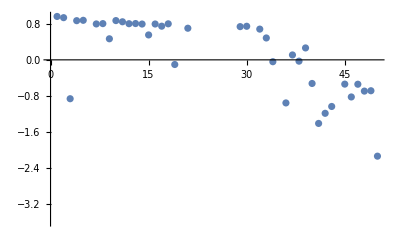

```mathematica
ListPlot[NSElist]
```

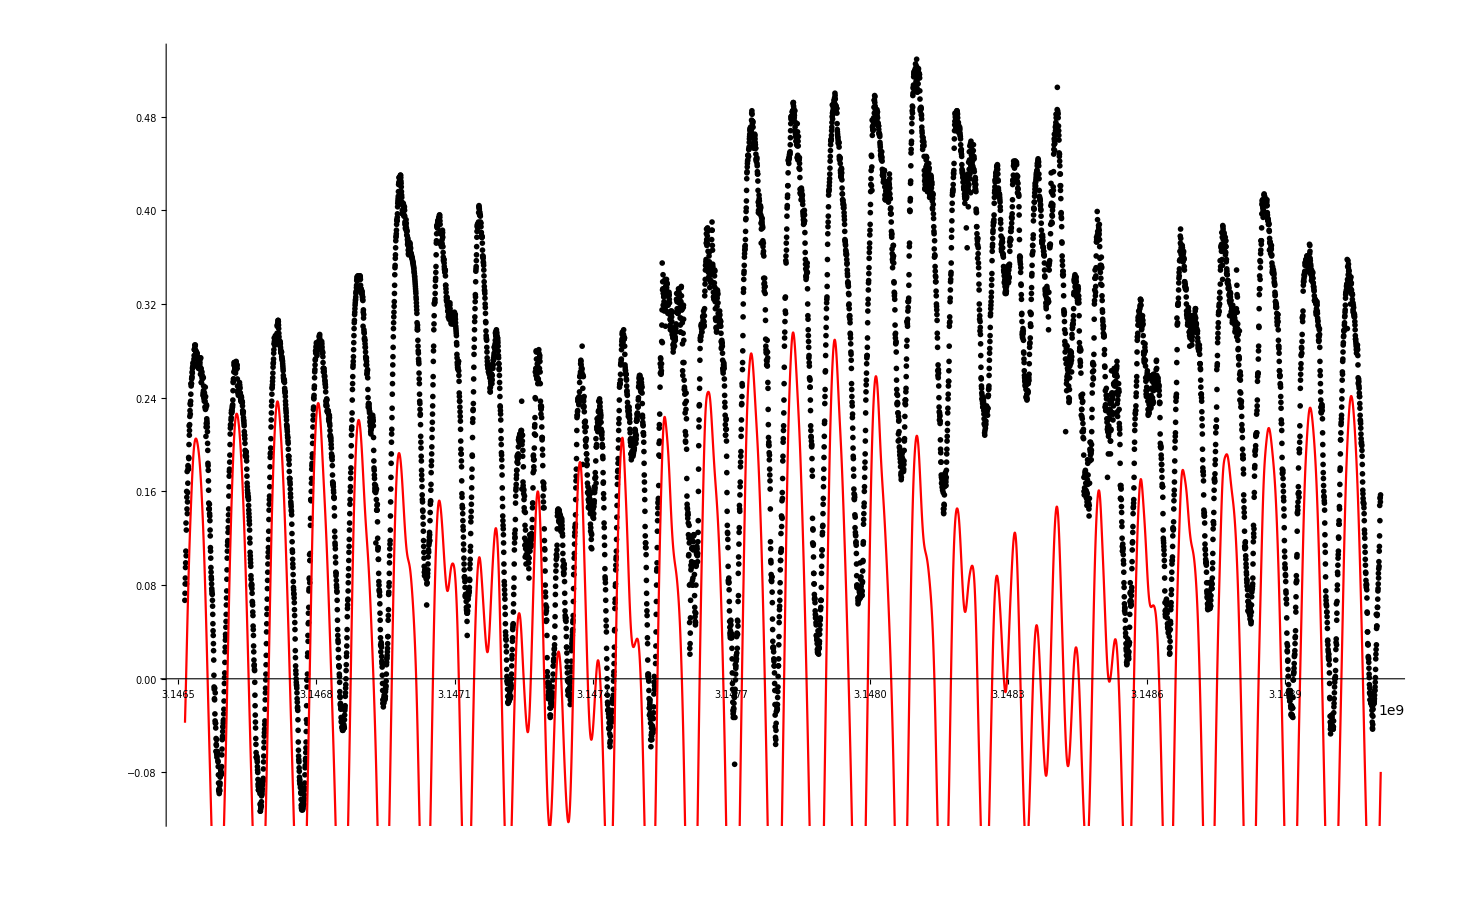

```mathematica
Show[ListPlot[ots[[50]],PlotStyle->Black],ListPlot[ts[[50]],Joined->True,PlotStyle->Red]]
```